## Лабораторная работа 5 Робилко Тимур, гр . 221701, Вариант 10

### Задание 1

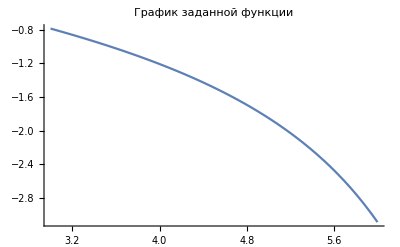

```mathematica
f[x_]:= Cot[Sqrt[x+2]];
Subscript[x, 0]=4.31;
initialPlot=Plot[f[x],{x, 3,6},PlotLabel -> "График заданной функции"];
Show[initialPlot]
```

#### а) функция D системы Mathematica

```mathematica
Print["Производная 1-го порядка: ", d1=D[f[x],x]/.x->Subscript[x, 0]]
Print["Производная 2-го порядка: ", d2=D[f[x],{x,2}]/.x->Subscript[x, 0] ]
```

Производная 1-го порядка: -0.574067

Производная 2-го порядка: -0.268199

#### б) формулы численного дифференцирования

```mathematica
FiniteDifference1[y_,y1_]:=y1-y; (* Функции конечных разностей 3-х порядков*)
FiniteDifference2[y_,y1_,y2_]:=y2-2y1+y;
FiniteDifference3[y_,y1_,y2_,y3_]:=y3-3y2+3y1-y;
```

```mathematica
h=0.1; (* Для шага 0.1 *)
```

```mathematica
y1=1/h(FiniteDifference1[f[Subscript[x, 0]],f[Subscript[x, 0]+h]]-1/2*FiniteDifference2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]+1/3*FiniteDifference3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]]);
```

```mathematica
y2=1/h^2(FiniteDifference2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]-FiniteDifference3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]]);
```

```mathematica
Print["Производная 1-го порядка: ", y1]
Print["Производная 2-го порядка: ", y2]

Print["Разница между вычисленными значениями 1-й производной: ",Abs[d1-y1]]
Print["Разница между вычисленными значениями 2-й производной: ",Abs[d2-y2]]
```

Производная 1-го порядка: -0.574145

Производная 2-го порядка: -0.265381

Разница между вычисленными значениями 1-й производной: 0.0000780577

Разница между вычисленными значениями 2-й производной: 0.00281786

```mathematica
h=0.01; (* Для шага 0.01 *)
```

```mathematica
y1=1/h(FiniteDifference1[f[Subscript[x, 0]],f[Subscript[x, 0]+h]]-1/2*FiniteDifference2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]+1/3*FiniteDifference3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]]);
y2=1/h^2(FiniteDifference2[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h]]-FiniteDifference3[f[Subscript[x, 0]],f[Subscript[x, 0]+h],f[Subscript[x, 0]+2h], f[Subscript[x, 0]+3h]]);
```

```mathematica
Print["Производная 1-го порядка: ", y1]
Print["Производная 2-го порядка: ", y2]

Print["Разница между вычисленными значениями 1-й производной: ",Abs[d1-y1]]
Print["Разница между вычисленными значениями 2-й производной: ",Abs[d2-y2]]
```

Производная 1-го порядка: -0.574067

Производная 2-го порядка: -0.268175

Разница между вычисленными значениями 1-й производной: 6.65807×10^-8

Разница между вычисленными значениями 2-й производной: 0.0000243751

Таким образом, уменьшение шага приводит к получению более точных результатов

### Задание 2

#### А)

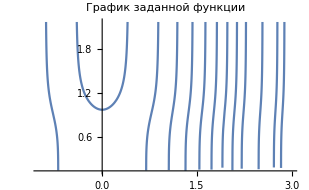

```mathematica
f[x_]:=Tan[5*x^2+7]^(1/4)
Plot[f[x], {x,-1,3},PlotLabel -> "График заданной функции"]
```

Так как изначальная функция определена не на всем множестве R, расчёты дают комплексные значения, которые невозможно будет сравнить.
Функция заменена на следующую для устранения разрывов и обеспечения области определения R :

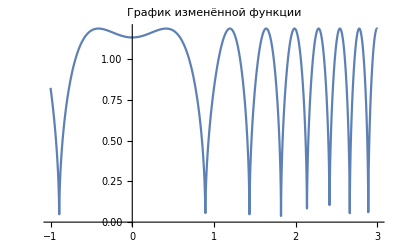

```mathematica
f[x_]:=(Sin[5*x^2+7]+1)^(1/4)
Plot[f[x], {x,-1,3},PlotLabel -> "График изменённой функции"]
```

```mathematica
a=-1;
b=3;
h=0.2;
data=Table[{x,(f[x+h]-f[x-h])/(2h)},{x,a,b,h}];
TableForm[data,TableHeadings->{None,{"x_i","y'_i"}}]
```

x_i | y'_i
-1. | -1.12188
-0.8 | 0.74236
-0.6 | 1.12208
-0.4 | 0.0881237
-0.2 | -0.136061
0. | 0.
0.2 | 0.136061
0.4 | -0.0881237
0.6 | -1.12208
0.8 | -0.74236
1. | 1.12188
1.2 | -0.615047
1.4 | -0.0710699
1.6 | -0.186353
1.8 | 0.0554573
2. | 1.09246
2.2 | -1.75482
2.4 | 0.171302
2.6 | 1.69305
2.8 | 0.442982
3. | 0.076906

#### Б)

```mathematica
Derivate=D[f[x],x]
```

(5 x Cos[7+5 x^2])/(2 (1+Sin[7+5 x^2])^(3/4))

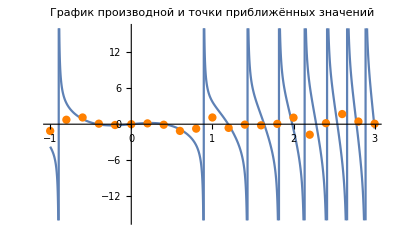

```mathematica
graph=Plot[Derivate,{x,-1,3}];
points=ListPlot[data,PlotStyle->{PointSize[0.015],Orange}];
Show[graph,points, PlotLabel-> "График производной и точки приближённых значений"]
```

### Задание 3

#### А) Метод средних прямоугольников

```mathematica
f[x_]:=(x+(5 x^2+1.6)^(1/3))/(0.4 x^2+√(1.9x+2))
a=0.3;
b=1.1;
Subscript[x, 0]=a;
```

```mathematica
n1=8;
step=(b-a)/n1;
For[i=1,i<=n1,i++, Subscript[x, i]=step+Subscript[x, i-1];]
AverageRectangle1=(b-a)/n1*∑_(i=1)^n1 f[Subscript[x, i-1]+(b-a)/(2*n1)]
```

0.89613

```mathematica
n2=10;
step=(b-a)/n2;
For[i=1,i<=n2,i++, Subscript[x, i]=step+Subscript[x, i-1];]
AverageRectangle2=(b-a)/n2*∑_(i=1)^n2 f[Subscript[x, i-1]+(b-a)/(2*n2)]
```

0.896072

Уточнение по Ричардсону

```mathematica
k=2;
Richardson=AverageRectangle2+n1^k/(n2^k-n1^k)(AverageRectangle2-AverageRectangle1)
```

0.895969

#### Б) Метод трапеций

```mathematica
n1=8;
Subscript[x, 0]=a;
step=(b-a)/n1;
For[i=1,i<=n1,i++, Subscript[x, i]=step+Subscript[x, i-1];]
Trapezoidal1=(b-a)/n1*(∑_(i=1)^(n1-1) f[Subscript[x, i]]+f[Subscript[x, 0]]/2+f[Subscript[x, n1]]/2)
```

0.895648

```mathematica
n2=10;
Subscript[x, 0]=a;
step=(b-a)/n2;
For[i=1,i<=n2,i++,
Subscript[x, i]=step+Subscript[x, i-1];]
Trapezoidal2=(b-a)/n2*(∑_(i=1)^(n2-1) f[Subscript[x, i]]+f[Subscript[x, 0]]/2+f[Subscript[x, n2]]/2)
```

0.895763

Уточнение по Ричардсону

```mathematica
Richardson=Trapezoidal2+n1^k/(n2^k-n1^k)(Trapezoidal2-Trapezoidal1)
```

0.89597

### Задание 4

#### Разбиение отрезка интегрирования на 8 частей

```mathematica
data=({{-0.5, -0.6966}, {-0.34, -0.4175}, {-0.18, -0.1994}, {-0.02, -0.0203}, {0.14, 0.1316}, {0.3, 0.2636}, {0.46, 0.3803}, {0.62, 0.4848}, {0.78, 0.5794}});
```

```mathematica
(* points=ListPlot[data,PlotStyle->{PointSize[0.015],Orange}, PlotLabel->"Заданная функция"];
Show[points] *)
```

```mathematica
a=-0.5;
b=0.78;
n=4;
h=(b-a)/(2n)
```

0.16

```mathematica
For[i=0,i<=2*n,i++, Subscript[y, i]=data[[i+1,2]];]
```

```mathematica
Simpsons=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
```

0.093344

#### Разбиение отрезка интегрирования на 16 частей

```mathematica
data=({{-0.5, -0.6966}, {-0.42, -0.5420}, {-0.34, -0.4175}, {-0.26, -0.2996}, {-0.18, -0.1994}, {-0.1, -0.1048}, {-0.02, -0.0203}, {0.06, 0.05797}, {0.14, 0.1316}, {0.22, 0.1978}, {0.3, 0.2636}, {0.38, 0.3204}, {0.46, 0.3803}, {0.54, 0.4296}, {0.62, 0.4848}, {0.7, 0.5279}, {0.78, 0.5794}});
```

```mathematica
n=8;
h=(b-a)/(2n)
For[i=0,i<=2*n,i++, Subscript[y, i]=data[[i+1,2]];]
```

0.08

```mathematica
Simpsons=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
```

0.0927488

### Задание 5

#### Формула Гаусса (4 узла)

```mathematica
f[x_]=(x-2*Sin[4x+3])/(1.6x+0.7);
a=1.5;
b=2.9;
n=4;
polynomial = LegendreP[n,x]
```

1/8 (3-30 x^2+35 x^4)

```mathematica
soluton=NSolve[polynomial==0,x];
xx=x/.soluton
```

{-0.861136,-0.339981,0.339981,0.861136}

```mathematica
T=Table[If[i==1,1,(xx[[j]])^(i-1)],{i,n},{j,n}];MatrixForm[T]
```

(1 | 1 | 1 | 1
-0.861136 | -0.339981 | 0.339981 | 0.861136
0.741556 | 0.115587 | 0.115587 | 0.741556
-0.638581 | -0.0392974 | 0.0392974 | 0.638581)

```mathematica
B=Table[If[EvenQ[i]==True,0,2/i],{i,n}]//N
```

{2.,0.,0.666667,0.}

```mathematica
A=LinearSolve[T,B]
```

{0.347855,0.652145,0.652145,0.347855}

```mathematica
Integral=(b-a)/2*∑_(i=1)^n A[[i]]*f[(b+a)/2+(b-a)/2*xx[[i]]]
```

0.825854